```mathematica
SetDirectory[NotebookDirectory[]];
Get["PhLib.wl"];
```

```mathematica
Catch[
file="LAB_23_06\\0.fasor";
res = PhLib`ReadPhasor[file];
(* PhLib`PolarDiagram[PhLib`scale[res[[1]]], "1381"] *)
]
```

```mathematica
file="BATEIAS_04-06\\0.fasor";
res = PhLib`ReadPhasor[file];
ds = PhLib`ReadHeadPhasors[file, 10, "Day"];
```

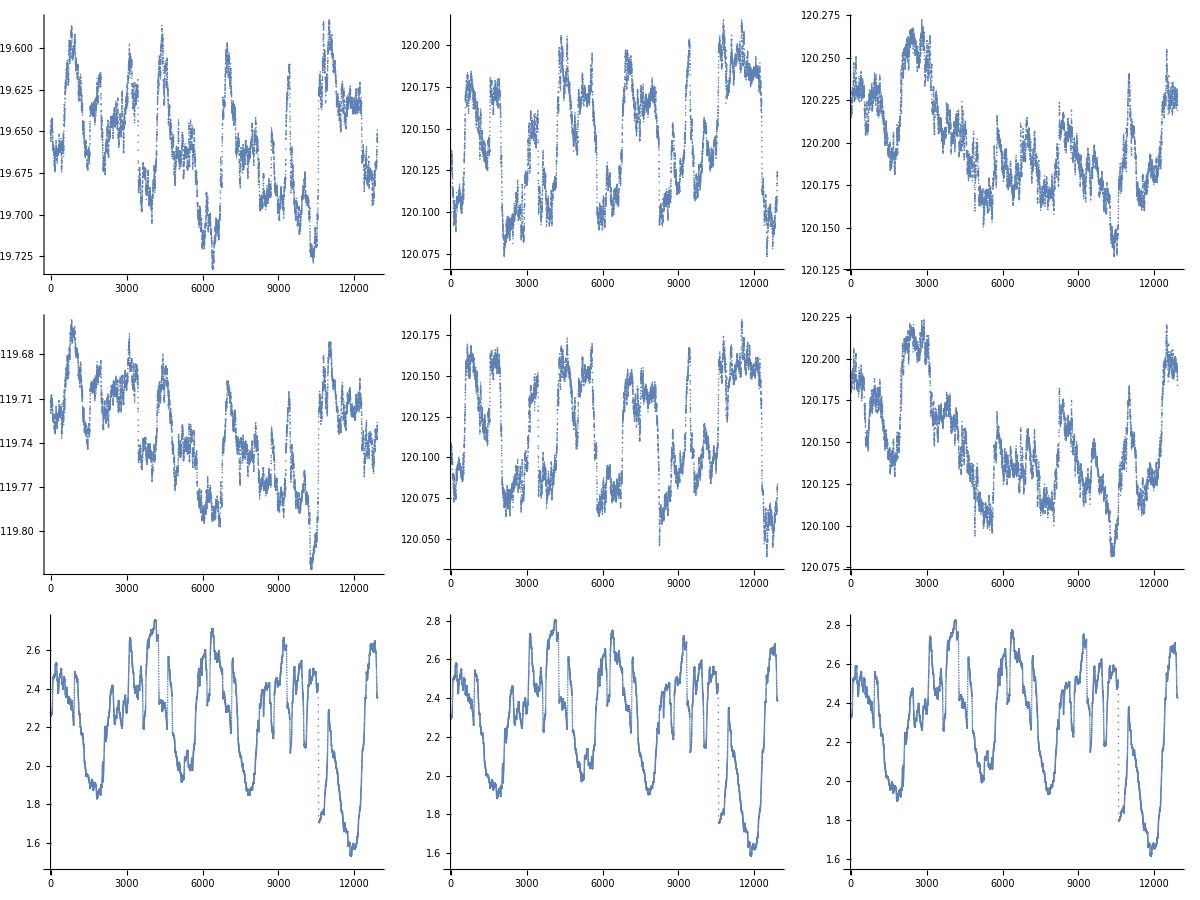

```mathematica
Grid[{{
ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"A138"]]-ds[[All,"C138"]] ),20],
ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"B138"]]-ds[[All,"C138"]] ),20],
ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"A138"]]-ds[[All,"B138"]] ),20]}
,
{ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"A230"]]-ds[[All,"C230"]] ),20],
ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"B230"]]-ds[[All,"C230"]] ),20],
ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"A230"]]-ds[[All,"B230"]] ),20]}
,
{ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"A230"]]-ds[[All,"A138"]] ),20],
ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"B230"]]-ds[[All,"B138"]] ),20],
ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"C230"]]-ds[[All,"C138"]] ),20]}
}]
```

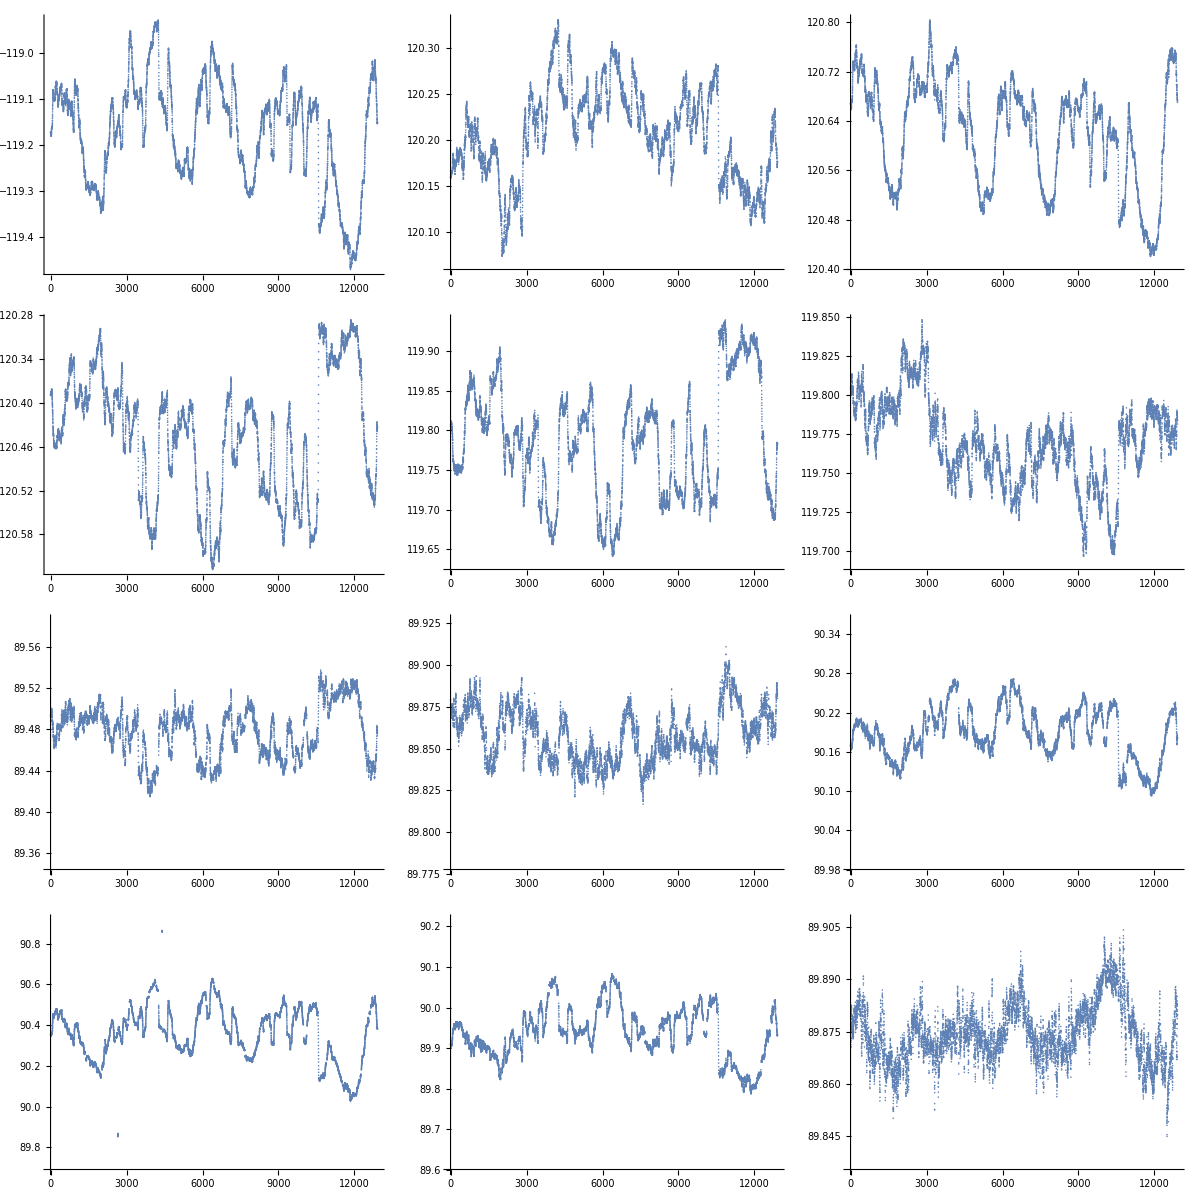

```mathematica
Grid[{{
ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"IA1381"]]-ds[[All,"IC1381"]] ),20],
ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"IB1381"]]-ds[[All,"IC1381"]] ),20],
ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"IA1381"]]-ds[[All,"IB1381"]] ),20]}
,
{ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"IA2301"]]-ds[[All,"IC2301"]] ),20],
ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"IB2301"]]-ds[[All,"IC2301"]] ),20],
ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"IA2301"]]-ds[[All,"IB2301"]] ),20]}
,
{ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"IA2301"]]-ds[[All,"A230"]] ),20],
ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"IB2301"]]-ds[[All,"B230"]] ),20],
ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"IC2301"]]-ds[[All,"C230"]] ),20]}
,
{ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"IA1381"]]-ds[[All,"A138"]] ),20],
ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"IB1381"]]-ds[[All,"B138"]] ),20],
ListPlot@MovingAverage[PhLib`toang /@ ( ds[[All,"IC1381"]]-ds[[All,"C138"]] ),20]}
}]
```

```mathematica
Compare[F1_, F2_, F3_] := 
Column[{
StringForm[ " `` vs `` = `` ", 
F1,F3, NumberForm[MedianDeviation[ PhLib`toang /@ ( ds[[All,F1]]-ds[[All,F3]] )],{3,4}]
],
StringForm[ " `` vs `` = `` ",
F2,F3, NumberForm[MedianDeviation[ PhLib`toang /@ ( ds[[All,F2]]-ds[[All,F3]] )],{3,4}]
],
StringForm[ " `` vs `` = `` ",
F1,F2, NumberForm[ MedianDeviation[ PhLib`toang /@ ( ds[[All,F1]]-ds[[All,F2]] )],{3,4}]
],
StringForm[ " `` vs `` ref `` ``",F1,F2,F3, 
NumberForm[Correlation[ 
PhLib`toang /@ ( ds[[All,F1]]-ds[[All,F3]] ),
PhLib`toang /@ ( ds[[All,F2]]-ds[[All,F3]] )],{3,4}]
],
StringForm[ " `` vs `` ref `` ``",F1,F3,F2, 
NumberForm[Correlation[ 
PhLib`toang /@ ( ds[[All,F1]]-ds[[All,F2]] ),
PhLib`toang /@ ( ds[[All,F3]]-ds[[All,F2]] )],{3,4}]
],
StringForm[ " `` vs `` ref `` ``",F2,F3,F1, 
NumberForm[Correlation[ 
PhLib`toang /@ ( ds[[All,F2]]-ds[[All,F1]] ),
PhLib`toang /@ ( ds[[All,F3]]-ds[[All,F1]] )],{3,4}]
]
}]
```

```mathematica
Grid[{
{Compare["IA1381","IB1381","IC1381"],
Compare["IA1382","IB1382","IC1382"]},
{Compare["IA2301","IB2301","IC2301"],
Compare["IA2302","IB2302","IC2302"]},
{Compare["A138","B138","C138"],
Compare["A230","B230","C230"]},
{Compare["IA1381","IA1382","A138"],
Compare["IA2301","IA2302","A230"]},
{Compare["IB1381","IB1382","B138"],
Compare["IB2301","IB2302","B230"]},
{Compare["IC1381","IC1382","C138"],
Compare["IC2301","IC2302","C230"]}
}, Frame->All]
```

IA1381 vs IC1381 = 0.0758 
 IB1381 vs IC1381 = 0.0374 
 IA1381 vs IB1381 = 0.0586 
 IA1381 vs IB1381 ref IC1381 0.6890
 IA1381 vs IC1381 ref IB1381 -0.3010
 IB1381 vs IC1381 ref IA1381 0.8990 |  IA1382 vs IC1382 = 0.0534 
 IB1382 vs IC1382 = 0.0598 
 IA1382 vs IB1382 = 0.0284 
 IA1382 vs IB1382 ref IC1382 0.8970
 IA1382 vs IC1382 ref IB1382 0.4530
 IB1382 vs IC1382 ref IA1382 -0.0128
 IA2301 vs IC2301 = 0.0647 
 IB2301 vs IC2301 = 0.0547 
 IA2301 vs IB2301 = 0.0218 
 IA2301 vs IB2301 ref IC2301 0.9310
 IA2301 vs IC2301 ref IB2301 -0.2370
 IB2301 vs IC2301 ref IA2301 0.5750 |  IA2302 vs IC2302 = 0.0445 
 IB2302 vs IC2302 = 0.0430 
 IA2302 vs IB2302 = 0.0231 
 IA2302 vs IB2302 ref IC2302 0.8160
 IA2302 vs IC2302 ref IB2302 0.0874
 IB2302 vs IC2302 ref IA2302 0.5040
 A138 vs C138 = 0.0269 
 B138 vs C138 = 0.0311 
 A138 vs B138 = 0.0219 
 A138 vs B138 ref C138 0.6190
 A138 vs C138 ref B138 0.4850
 B138 vs C138 ref A138 0.3860 |  A230 vs C230 = 0.0264 
 B230 vs C230 = 0.0308 
 A230 vs B230 = 0.0241 
 A230 vs B230 ref C230 0.5490
 A230 vs C230 ref B230 0.4850
 B230 vs C230 ref A230 0.4640
 IA1381 vs A138 = 0.0904 
 IA1382 vs A138 = 0.0685 
 IA1381 vs IA1382 = 0.0240 
 IA1381 vs IA1382 ref A138 0.9670
 IA1381 vs A138 ref IA1382 -0.0267
 IA1382 vs A138 ref IA1381 -0.0003 |  IA2301 vs A230 = 0.0222 
 IA2302 vs A230 = 0.0221 
 IA2301 vs IA2302 = 0.0067 
 IA2301 vs IA2302 ref A230 0.9670
 IA2301 vs A230 ref IA2302 -0.0268
 IA2302 vs A230 ref IA2301 -0.0002
 IB1381 vs B138 = 0.0443 
 IB1382 vs B138 = 0.0769 
 IB1381 vs IB1382 = 0.0345 
 IB1381 vs IB1382 ref B138 0.9670
 IB1381 vs B138 ref IB1382 -0.0269
 IB1382 vs B138 ref IB1381 0.0001 |  IB2301 vs B230 = 0.0163 
 IB2302 vs B230 = 0.0142 
 IB2301 vs IB2302 = 0.0070 
 IB2301 vs IB2302 ref B230 0.9670
 IB2301 vs B230 ref IB2302 -0.0266
 IB2302 vs B230 ref IB2301 -0.0004
 IC1381 vs C138 = 0.0117 
 IC1382 vs C138 = 0.0147 
 IC1381 vs IC1382 = 0.0054 
 IC1381 vs IC1382 ref C138 0.9670
 IC1381 vs C138 ref IC1382 -0.0268
 IC1382 vs C138 ref IC1381 -0.0003 |  IC2301 vs C230 = 0.0304 
 IC2302 vs C230 = 0.0137 
 IC2301 vs IC2302 = 0.0198 
 IC2301 vs IC2302 ref C230 0.9670
 IC2301 vs C230 ref IC2302 -0.0265
 IC2302 vs C230 ref IC2301 -0.0005

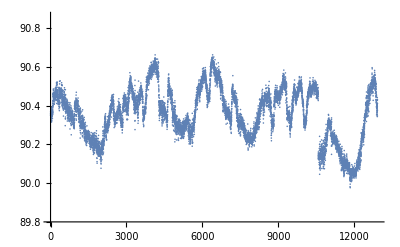
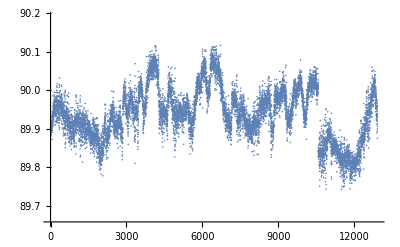
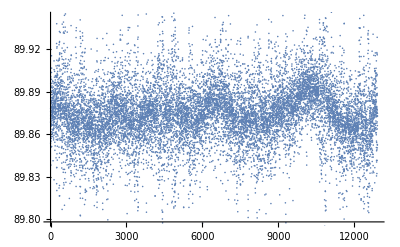
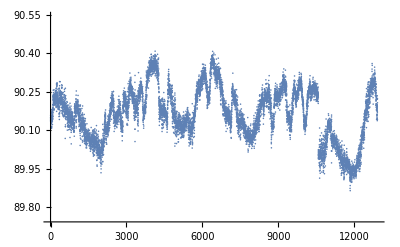
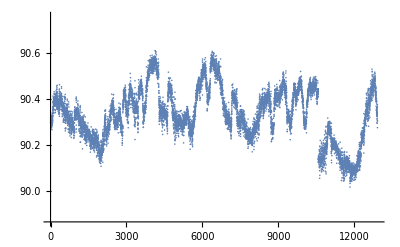
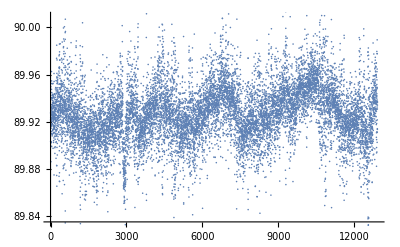
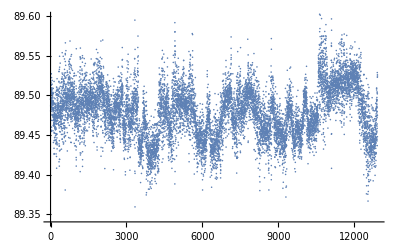
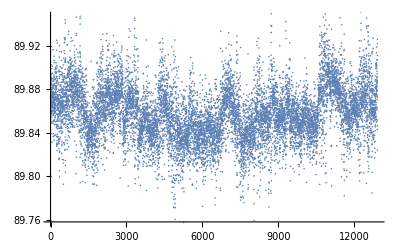
-Graphics-X1 - FASE A | -Graphics-X1 - FASE B | -Graphics-X1 - FASE C
-Graphics-X2 - FASE A | -Graphics-X2 - FASE B | -Graphics-X2 - FASE C
-Graphics-H1 - FASE A | -Graphics-H1 - FASE B | -Graphics-H1 - FASE C
-Graphics-H2 - FASE A | -Graphics-H2 - FASE B | -Graphics-H2 - FASE C

```mathematica
Grid[{
{Labeled[ListPlot[PhLib`toang /@ (ds[[All,"IA1381"]]-ds[[All,"A138"]]), PlotRange->Automatic], "X1 - FASE A"],
Labeled[ListPlot[PhLib`toang /@ (ds[[All,"IB1381"]]-ds[[All,"B138"]]), PlotRange->Automatic], "X1 - FASE B"],
Labeled[ListPlot[PhLib`toang /@ (ds[[All,"IC1381"]]-ds[[All,"C138"]]), PlotRange->Automatic], "X1 - FASE C"]},
{Labeled[ListPlot[PhLib`toang /@ (ds[[All,"IA1382"]]-ds[[All,"A138"]]), PlotRange->Automatic], "X2 - FASE A"],
Labeled[ListPlot[PhLib`toang /@ (ds[[All,"IB1382"]]-ds[[All,"B138"]]), PlotRange->Automatic], "X2 - FASE B"],
Labeled[ListPlot[PhLib`toang /@ (ds[[All,"IC1382"]]-ds[[All,"C138"]]), PlotRange->Automatic], "X2 - FASE C"]},
{Labeled[ListPlot[PhLib`toang /@ (ds[[All,"IA2301"]]-ds[[All,"A230"]]), PlotRange->Automatic], "H1 - FASE A"],
Labeled[ListPlot[PhLib`toang /@ (ds[[All,"IB2301"]]-ds[[All,"B230"]]), PlotRange->Automatic], "H1 - FASE B"],
Labeled[ListPlot[PhLib`toang /@ (ds[[All,"IC2301"]]-ds[[All,"C230"]]), PlotRange->Automatic], "H1 - FASE C"]},
{Labeled[ListPlot[PhLib`toang /@ (ds[[All,"IA2302"]]-ds[[All,"A230"]]), PlotRange->Automatic], "H2 - FASE A"],
Labeled[ListPlot[PhLib`toang /@ (ds[[All,"IB2302"]]-ds[[All,"B230"]]), PlotRange->Automatic], "H2 - FASE B"],
Labeled[ListPlot[PhLib`toang /@ (ds[[All,"IC2302"]]-ds[[All,"C230"]]), PlotRange->Automatic], "H2 - FASE C"]}
}]
```

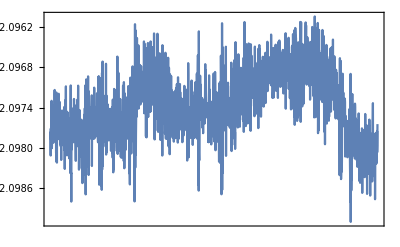

{}

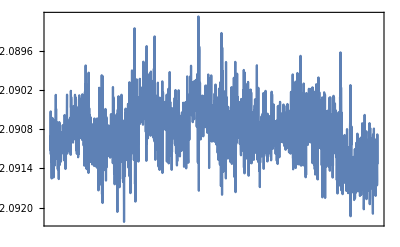

{}

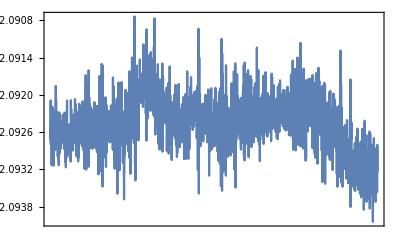

```mathematica
res = {};
Do [ AppendTo[res, PhLib`PolarData[PhLib`scale[d],"230"] ], {d,ds}];
DateListPlot[Table[ {r[[1]], r[[2,2,1]]}, {r,res}]]
res = {}
Do [ AppendTo[res, PhLib`PolarData[PhLib`scale[d],"2301"] ], {d,ds}];
DateListPlot[Table[ {r[[1]], r[[2,2,1]]}, {r,res}]]
res = {}
Do [ AppendTo[res, PhLib`PolarData[PhLib`scale[d],"2302"] ], {d,ds}];
DateListPlot[Table[ {r[[1]], r[[2,2,1]]}, {r,res}]]
```